```mathematica
SEMINARSKA NALOGA



																				





																RACIONALNE FUNKCIJE











													RAČUNALNIŠKA ORODJA V MATEMATIKI 2019/20


																																																																								
																															AVTORICA: MARTINA SPASIĆ
```

KAJ SO RACIONALNE FUNKCIJE?

Racionalne funkcije so funkcije, ki jih lahko zapišemo v obliki ulomka, kjer sta v števcu in imenovalcu polinoma. Pri tem prevzamemo, da polinom v imenovalcu ni enak nič. 
Takšna funkcija je definirana za vsak x razen za tistega, ki je ničla polinoma v imenovalcu.
Definicija osnovnega izreka algebre (Gaussov izrek) pravi, da ima vsak nekonstanten polinom ene spremenljivke stopnje n s kompleksnimi koeficienti vsaj eno kompleksno ničlo in čigava posledica je dejstvo, da lahko poljuben polinom stopnje n (n > 0) faktoriziramo - zapišemo v obliki produkta:
												
												  p(x) = a(x - x1)(x - x2) ... (x - xn)
												
													a : vodilni koeficient
													x1,  x2, ..., xn : ničle polinoma
													
Po tem izreku lahko polinom v števcu in imenovalcu razcepimo. Če je ulomek okrajšan, dobimo v števcu ničle racionalne funkcije, v imenovalcu pa pole. V polih se graf pretrga in se približuje navpični asimptoti.
Ko gre x proti neskončno ali proti minus neskončno, se racionalna funkcija približuje asimtotskemu polinomu k(x), ki ga dobimo kot količnik pri deljenju števca z imenovalcem. Pri tem deljenju dobimo tudi ostanek - če obstaja točka, kjer je ostanek enak 0, potem tam funkcija seka asimptotski polinom. Če je asimptotski polinom prve stopnje, ga imenujemo asimptotska premica oziroma (glavna) asimptota.

GRAF  RACIONALNE FUNKCIJE

Funkcija je zvezna povsod, kjer je definirana, kar pomeni, da se graf pretrga samo v polih.
Pri risanju grafa upoštevamo naslednja pravila:

1) graf racionalne funkcije, ko gre x proti +/- neskončno
	a) če je stopnja imenovalca večja od stopnje števca, se graf funkcije, ko se oddaljujemo od izhodišča koordinatnega sistema približuje abcisni osi, torej ima vodoravno asimptoto y = 0.
	b) v splošnem pa števec funkcije delimo z imenovalcem, pri čemer dobimo količnik in ostanek. Dobljeni količnik imenujemo asimptotski polinom. Grafu tega polinoma se graf racionalne funkcije približuje, ko se oddaljujemo od izhodišča koordinatnega sistema. Pogosto je asimptotski polinom prve ali ničte stopnje in ima za graf premico.Graf včasih tudi seka asimptoto - presečišča so v točkah, kjer je ostanek pri deljenju števca z imenovalcem enak 0.

2) Graf racionalne funkcije v okolici ničle k-te stopnje narišemo enako kot graf polinoma v okolici ničle k-te stopnje.

3)Graf racionalne funkcije v okolici pola k-te stopnje je podoben kot graf potenčne funkcije y = x −k (z ustreznim raztegom in premikom).
To pomeni, da se graf v okolici pola vedno približuje navpični asimptoti, glede predznaka funkcije pa ločimo dve vrsti polov:
	a) V polih lihe stopnje se predznak funkcije spremeni.
	b) v polih sode stopnje se predznak funkcije ohrani.
Predznak racionalne funkcije se spremeni samo v polih in ničlah lihe stopnje.

PRIMERI NALOG

1.  naloga
Nariši graf funkcije q(x):=(x^6+2 x^3+1)/(x^6-3 x^4+x^2-3).

Najprej bom izračunala ničle podane racionalne funkcije. To naredim tako, da rešim enačbo q(x) = 0.

```mathematica
q[x_]:=(x^6 + 2*x^3 + 1) / (x^6 - 3*x^4 + x^2 - 3)

nicle = Solve[q[x] == 0, x]
```

{{x→-1},{x→-1},{x→(-1)^(1/3)},{x→(-1)^(1/3)},{x→-(-1)^(2/3)},{x→-(-1)^(2/3)}}

Ko rešim enačbo, kjer imenovalec funkcije enačim z 0, dobimo pole.

```mathematica
polix = Solve[Denominator[q[x]] == 0]
```

{{x→-(-1)^(1/4)},{x→(-1)^(1/4)},{x→-(-1)^(3/4)},{x→(-1)^(3/4)},{x→-√3},{x→√3}}

```mathematica
poli = x/.polix
```

{-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4),-√3,√3}

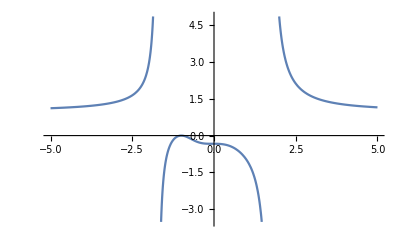

```mathematica
Plot[q[x],{x,-5,5}]
```

S pomočjo ukaza plot pa dobim še graf funkcije q(x).

2. naloga
 Nariši funkcijo f(x) = (1 - x^2) / (x^2  + 1). Določi ničle, pole, nariši graf. Izračunaj presečišče s funkcijo g(x) = x^2 - 1,  izračunaj ploščino lika, ki nastane kot njun presek ter nariši obe funkciji na isti graf.

```mathematica
f[x_]:=(1 -x^2) / (x^2 + 1)
```

```mathematica
nicle1 = Solve[f[x]==0, x]
```

{{x→-1},{x→1}}

```mathematica
polif=Solve[Denominator[f[x]]==0]
```

{{x→-ⅈ},{x→ⅈ}}

Ko imenovalec enačim z 0, ne dobim realnih rešitev.

```mathematica
poli1=x/.polif
```

{-ⅈ,ⅈ}

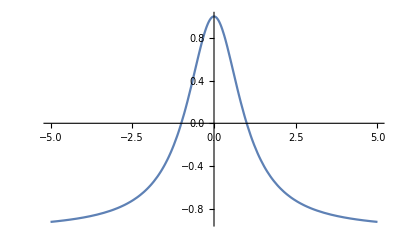

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
g[x_] := x^2 - 1
```

```mathematica
Solve[g[x]==f[x],x]
```

{{x→-1},{x→1},{x→-ⅈ √2},{x→ⅈ √2}}

Izračunam presečišča funkcij f(x) in g(x), tako da rešim enačbo f(x) = g(x).

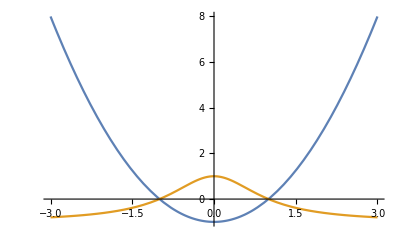

```mathematica
graf=Plot[{g[x],f[x]},{x,-3,3}]
```

```mathematica
Integrate[f[x]-g[x],{x,-1,1}]
```

-2/3+π

```mathematica
N[Integrate[f[x]-g[x],{x,-1,1}]]
```

2.47493

Približna vrednost ploščine lika med obema grafoma je 2.47493.

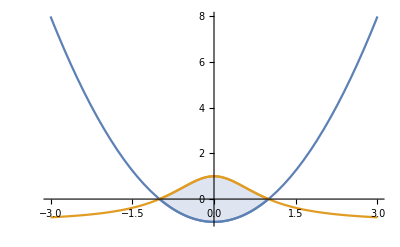

```mathematica
Show[graf,Plot[{g[x],f[x]},{x,-1,1},Filling-> {1 -> {2}}]]
```

```mathematica
Show[%29,Background->Directive[RGBColor[1.,0.9500000000000001,0.8300000000000001],Opacity[1.]]]
```

-Graphics-

Določen integral  zveznih funkcij f(x) in g(x) na intervalu [-1, 1] je enak ploščini lika, ki ga predstavlja presek že omenjenih grafov, kar se vidi na zgornji sliki.

VIRI:
a) https://sl.wikipedia.org/wiki/Racionalna_funkcija
b) http://www2.arnes.si/~mpavle1/mp/rac_f.html
c) https://ucilnica.fmf.uni-lj.si/course/view.php?id=131